# SVM-BDS-BDT Comparison Results, 5/19/16

## Raw Data

## SVM: c, γ, Number of Support Vectors, False Positive Fraction, False Negative Fraction, Efficiency

```mathematica
SVMLinearHardRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","linearhard0519"}], "Table"];
SVMLinearSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","linearsoft0519"}], "Table"];

SVMCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","circlehard0519"}], "Table"];
SVMCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","circlesoft0519"}], "Table"];

SVMTwoCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","twocirclehard0519"}], "Table"]
SVMTwoCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","twocirclesoft0519"}], "Table"];
```

{{0.001,1.,412,0.,1.,0.},{0.001,1.5,416,0.,1.,0.},{0.001,2.,418,0.,1.,0.},{0.001,2.5,417,0.,1.,0.},{0.001,3.,421,0.,1.,0.},{0.001,3.5,422,0.,1.,0.},{0.001,4.,422,0.,1.,0.},{0.001,4.5,424,0.,1.,0.},{0.001,5.,423,0.,1.,0.},{0.001,5.5,424,0.,1.,0.},{0.001,6.,427,0.,1.,0.},{0.00177828,1.,421,0.,1.,0.},{0.00177828,1.5,424,0.,1.,0.},{0.00177828,2.,432,0.,1.,0.},{0.00177828,2.5,438,0.,1.,0.},{0.00177828,3.,442,0.,1.,0.},{0.00177828,3.5,444,0.,1.,0.},{0.00177828,4.,445,0.,1.,0.},{0.00177828,4.5,452,0.,1.,0.},{0.00177828,5.,459,0.,1.,0.},{0.00177828,5.5,469,0.,1.,0.},{0.00177828,6.,481,0.,1.,0.},{0.00316228,1.,430,0.,1.,0.},{0.00316228,1.5,440,0.,1.,0.},{0.00316228,2.,451,0.,1.,0.},{0.00316228,2.5,461,0.,1.,0.},{0.00316228,3.,472,0.,1.,0.},{0.00316228,3.5,474,0.,1.,0.},{0.00316228,4.,491,0.,1.,0.},{0.00316228,4.5,518,0.,1.,0.},{0.00316228,5.,516,0.,1.,0.},{0.00316228,5.5,529,0.,1.,0.},{0.00316228,6.,545,0.,1.,0.},{0.00562341,1.,446,0.,1.,0.},{0.00562341,1.5,461,0.,1.,0.},{0.00562341,2.,481,0.,1.,0.},{0.00562341,2.5,496,0.,1.,0.},{0.00562341,3.,501,0.,1.,0.},{0.00562341,3.5,518,0.,1.,0.},{0.00562341,4.,537,0.,1.,0.},{0.00562341,4.5,553,0.,1.,0.},{0.00562341,5.,565,0.,1.,0.},{0.00562341,5.5,582,0.,1.,0.},{0.00562341,6.,598,0.,1.,0.},{0.01,1.,456,0.,1.,0.},{0.01,1.5,474,0.,1.,0.},{0.01,2.,513,0.,1.,0.},{0.01,2.5,522,0.,1.,0.},{0.01,3.,531,0.,1.,0.},{0.01,3.5,568,0.,1.,0.},{0.01,4.,583,0.,1.,0.},{0.01,4.5,600,0.,1.,0.},{0.01,5.,619,0.,1.,0.},{0.01,5.5,636,0.,1.,0.},{0.01,6.,647,0.,1.,0.},{0.0177828,1.,464,0.,1.,0.},{0.0177828,1.5,492,0.,1.,0.},{0.0177828,2.,533,0.,1.,0.},{0.0177828,2.5,557,0.,1.,0.},{0.0177828,3.,578,0.,1.,0.},{0.0177828,3.5,588,0.,1.,0.},{0.0177828,4.,621,0.,1.,0.},{0.0177828,4.5,643,0.,1.,0.},{0.0177828,5.,648,0.,1.,0.},{0.0177828,5.5,674,0.,1.,0.},{0.0177828,6.,674,0.,1.,0.},{0.0316228,1.,468,0.,0.789744,0.210256},{0.0316228,1.5,514,0.,1.,0.},{0.0316228,2.,552,0.,1.,0.},{0.0316228,2.5,571,0.,1.,0.},{0.0316228,3.,598,0.,1.,0.},{0.0316228,3.5,626,0.,1.,0.},{0.0316228,4.,646,0.,1.,0.},{0.0316228,4.5,660,0.,1.,0.},{0.0316228,5.,669,0.,1.,0.},{0.0316228,5.5,690,0.,1.,0.},{0.0316228,6.,697,0.,1.,0.},{0.0562341,1.,465,0.,0.364103,0.635897},{0.0562341,1.5,510,0.,0.533333,0.466667},{0.0562341,2.,558,0.,0.712821,0.287179},{0.0562341,2.5,584,0.,0.923077,0.0769231},{0.0562341,3.,613,0.,1.,0.},{0.0562341,3.5,642,0.,1.,0.},{0.0562341,4.,641,0.,1.,0.},{0.0562341,4.5,675,0.,1.,0.},{0.0562341,5.,692,0.,1.,0.},{0.0562341,5.5,703,0.,1.,0.},{0.0562341,6.,713,0.,1.,0.},{0.1,1.,397,0.00745342,0.153846,0.846154},{0.1,1.5,474,0.00124224,0.189744,0.810256},{0.1,2.,550,0.,0.25641,0.74359},{0.1,2.5,594,0.,0.358974,0.641026},{0.1,3.,614,0.,0.482051,0.517949},{0.1,3.5,646,0.,0.589744,0.410256},{0.1,4.,656,0.,0.712821,0.287179},{0.1,4.5,672,0.,0.841026,0.158974},{0.1,5.,687,0.,0.94359,0.0564103},{0.1,5.5,705,0.,0.984615,0.0153846},{0.1,6.,713,0.,1.,0.},{0.177828,1.,328,0.00869565,0.0974359,0.902564},{0.177828,1.5,393,0.00869565,0.0974359,0.902564},{0.177828,2.,477,0.00621118,0.107692,0.892308},{0.177828,2.5,537,0.00496894,0.123077,0.876923},{0.177828,3.,581,0.00124224,0.153846,0.846154},{0.177828,3.5,633,0.00124224,0.184615,0.815385},{0.177828,4.,651,0.,0.220513,0.779487},{0.177828,4.5,665,0.,0.271795,0.728205},{0.177828,5.,682,0.,0.338462,0.661538},{0.177828,5.5,702,0.,0.4,0.6},{0.177828,6.,711,0.,0.482051,0.517949},{0.316228,1.,269,0.00993789,0.0820513,0.917949},{0.316228,1.5,347,0.00993789,0.0717949,0.928205},{0.316228,2.,416,0.00993789,0.0717949,0.928205},{0.316228,2.5,479,0.00993789,0.0717949,0.928205},{0.316228,3.,524,0.00745342,0.0769231,0.923077},{0.316228,3.5,557,0.00745342,0.0769231,0.923077},{0.316228,4.,614,0.00496894,0.0769231,0.923077},{0.316228,4.5,629,0.00621118,0.0820513,0.917949},{0.316228,5.,657,0.00621118,0.0974359,0.902564},{0.316228,5.5,672,0.00372671,0.117949,0.882051},{0.316228,6.,685,0.00248447,0.133333,0.866667},{0.562341,1.,236,0.0161491,0.0615385,0.938462},{0.562341,1.5,294,0.0173913,0.0666667,0.933333},{0.562341,2.,363,0.0161491,0.0615385,0.938462},{0.562341,2.5,429,0.0124224,0.0615385,0.938462},{0.562341,3.,469,0.0124224,0.0615385,0.938462},{0.562341,3.5,506,0.0111801,0.0615385,0.938462},{0.562341,4.,552,0.0111801,0.0615385,0.938462},{0.562341,4.5,583,0.0111801,0.0615385,0.938462},{0.562341,5.,606,0.0111801,0.0615385,0.938462},{0.562341,5.5,628,0.0111801,0.0666667,0.933333},{0.562341,6.,652,0.0111801,0.0717949,0.928205},{1.,1.,203,0.0149068,0.0615385,0.938462},{1.,1.5,251,0.0149068,0.0512821,0.948718},{1.,2.,323,0.0136646,0.0512821,0.948718},{1.,2.5,396,0.0149068,0.0512821,0.948718},{1.,3.,442,0.0149068,0.0410256,0.958974},{1.,3.5,474,0.0136646,0.0410256,0.958974},{1.,4.,519,0.0124224,0.0410256,0.958974},{1.,4.5,542,0.0124224,0.0358974,0.964103},{1.,5.,573,0.0124224,0.0358974,0.964103},{1.,5.5,594,0.0124224,0.0358974,0.964103},{1.,6.,618,0.0124224,0.0410256,0.958974},{1.77828,1.,190,0.0186335,0.0512821,0.948718},{1.77828,1.5,229,0.0149068,0.0461538,0.953846},{1.77828,2.,289,0.0149068,0.0358974,0.964103},{1.77828,2.5,364,0.0161491,0.0410256,0.958974},{1.77828,3.,420,0.0161491,0.0307692,0.969231},{1.77828,3.5,448,0.0161491,0.0307692,0.969231},{1.77828,4.,491,0.0161491,0.0307692,0.969231},{1.77828,4.5,526,0.0161491,0.0307692,0.969231},{1.77828,5.,546,0.0149068,0.0307692,0.969231},{1.77828,5.5,565,0.0149068,0.0358974,0.964103},{1.77828,6.,598,0.0149068,0.0358974,0.964103},{3.16228,1.,152,0.0161491,0.0461538,0.953846},{3.16228,1.5,214,0.0173913,0.0410256,0.958974},{3.16228,2.,284,0.0149068,0.0410256,0.958974},{3.16228,2.5,345,0.0149068,0.0307692,0.969231},{3.16228,3.,393,0.0149068,0.0307692,0.969231},{3.16228,3.5,434,0.0161491,0.025641,0.974359},{3.16228,4.,470,0.0149068,0.025641,0.974359},{3.16228,4.5,498,0.0149068,0.0307692,0.969231},{3.16228,5.,534,0.0136646,0.025641,0.974359},{3.16228,5.5,556,0.0149068,0.025641,0.974359},{3.16228,6.,584,0.0149068,0.0307692,0.969231},{5.62341,1.,134,0.0186335,0.0512821,0.948718},{5.62341,1.5,198,0.0186335,0.0512821,0.948718},{5.62341,2.,260,0.0136646,0.0307692,0.969231},{5.62341,2.5,318,0.0136646,0.0307692,0.969231},{5.62341,3.,371,0.0136646,0.0307692,0.969231},{5.62341,3.5,423,0.0136646,0.0307692,0.969231},{5.62341,4.,458,0.0136646,0.0307692,0.969231},{5.62341,4.5,482,0.0136646,0.0307692,0.969231},{5.62341,5.,515,0.0136646,0.0307692,0.969231},{5.62341,5.5,554,0.0136646,0.0307692,0.969231},{5.62341,6.,574,0.0124224,0.0307692,0.969231},{10.,1.,118,0.0136646,0.0512821,0.948718},{10.,1.5,183,0.0149068,0.0410256,0.958974},{10.,2.,246,0.0161491,0.0307692,0.969231},{10.,2.5,311,0.0111801,0.0307692,0.969231},{10.,3.,373,0.0149068,0.0358974,0.964103},{10.,3.5,418,0.0149068,0.0358974,0.964103},{10.,4.,444,0.0149068,0.0307692,0.969231},{10.,4.5,474,0.0149068,0.0307692,0.969231},{10.,5.,505,0.0136646,0.0307692,0.969231},{10.,5.5,541,0.0149068,0.0307692,0.969231},{10.,6.,573,0.0149068,0.0307692,0.969231},{17.7828,1.,84,0.0149068,0.0410256,0.958974},{17.7828,1.5,170,0.0124224,0.0307692,0.969231},{17.7828,2.,250,0.0124224,0.0358974,0.964103},{17.7828,2.5,298,0.0149068,0.0358974,0.964103},{17.7828,3.,358,0.0161491,0.0307692,0.969231},{17.7828,3.5,406,0.0149068,0.0307692,0.969231},{17.7828,4.,434,0.0149068,0.025641,0.974359},{17.7828,4.5,473,0.0149068,0.0307692,0.969231},{17.7828,5.,501,0.0149068,0.0307692,0.969231},{17.7828,5.5,540,0.0161491,0.0307692,0.969231},{17.7828,6.,569,0.0161491,0.0307692,0.969231},{31.6228,1.,49,0.0124224,0.0358974,0.964103},{31.6228,1.5,165,0.0111801,0.0358974,0.964103},{31.6228,2.,238,0.0136646,0.0307692,0.969231},{31.6228,2.5,297,0.0161491,0.0307692,0.969231},{31.6228,3.,365,0.0161491,0.0307692,0.969231},{31.6228,3.5,405,0.0149068,0.0358974,0.964103},{31.6228,4.,432,0.0149068,0.0307692,0.969231},{31.6228,4.5,471,0.0149068,0.0307692,0.969231},{31.6228,5.,502,0.0149068,0.0307692,0.969231},{31.6228,5.5,538,0.0161491,0.0307692,0.969231},{31.6228,6.,573,0.0161491,0.0307692,0.969231},{56.2341,1.,43,0.0124224,0.0358974,0.964103},{56.2341,1.5,159,0.0111801,0.0307692,0.969231},{56.2341,2.,237,0.0136646,0.025641,0.974359},{56.2341,2.5,300,0.0161491,0.025641,0.974359},{56.2341,3.,362,0.0161491,0.025641,0.974359},{56.2341,3.5,410,0.0149068,0.0307692,0.969231},{56.2341,4.,435,0.0149068,0.0307692,0.969231},{56.2341,4.5,471,0.0149068,0.0307692,0.969231},{56.2341,5.,502,0.0149068,0.0307692,0.969231},{56.2341,5.5,538,0.0161491,0.0307692,0.969231},{56.2341,6.,573,0.0161491,0.0307692,0.969231},{100.,1.,41,0.0124224,0.0358974,0.964103},{100.,1.5,165,0.0111801,0.0358974,0.964103},{100.,2.,234,0.0136646,0.025641,0.974359},{100.,2.5,304,0.0161491,0.025641,0.974359},{100.,3.,362,0.0161491,0.025641,0.974359},{100.,3.5,410,0.0149068,0.0307692,0.969231},{100.,4.,435,0.0149068,0.0307692,0.969231},{100.,4.5,471,0.0149068,0.0307692,0.969231},{100.,5.,502,0.0149068,0.0307692,0.969231},{100.,5.5,538,0.0161491,0.0307692,0.969231},{100.,6.,573,0.0161491,0.0307692,0.969231}}

## BDS: Number of Stumps, Efficiency, False Positive Fraction, False Negative Fraction

```mathematica
BDSLinearHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","linearhard0519"}], "Table"];
BDSLinearSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","linearsoft0519"}], "Table"];

BDSCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","circlehard0519"}], "Table"];
BDSCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","circlesoft0519"}], "Table"];

BDSTwoCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","twocirclehard0519"}], "Table"];
BDSTwoCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","twocirclesoft0519"}], "Table"];
```

Import::nffil: File not found during Import.

## BDT: Number of Trees, Efficiency, False Positive Fraction, False Negative Fraction

```mathematica
BDTLinearHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","linearhard0519"}], "Table"];
BDTLinearSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","linearsoft0519"}], "Table"];

BDTCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","circlehard0519"}], "Table"];
BDTCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","circlesoft0519"}], "Table"];

BDTTwoCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","twocirclehard0519"}], "Table"];
BDTTwoCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","twocirclesoft0519"}], "Table"];
```

Import::nffil: File not found during Import.

## Formatted Datasets

## SVM

### c-γ-Efficiency

```mathematica
SVMLinearHardCGE = SVMLinearHardRawData[[All,{1,2, 6}]];
SVMLinearSoftCGE = SVMLinearSoftRawData[[All,{1,2, 6}]];

SVMCircleHardCGE = SVMCircleHardRawData[[All,{1,2, 6}]];
SVMCircleSoftCGE = SVMCircleSoftRawData[[All,{1,2, 6}]];

SVMTwoCircleHardCGE = SVMTwoCircleHardRawData[[All,{1,2, 6}]];
SVMTwoCircleSoftCGE = SVMTwoCircleSoftRawData[[All,{1,2, 6}]];
```

### Log(c)-γ-Efficiency

```mathematica
SVMLinearHardLogCGE = MapAt[Log10, SVMLinearHardCGE, {All, 1}];
SVMLinearSoftLogCGE = MapAt[Log10, SVMLinearSoftCGE, {All, 1}];

SVMCircleHardLogCGE = MapAt[Log10, SVMCircleHardCGE, {All, 1}];
SVMCircleSoftLogCGE = MapAt[Log10, SVMCircleSoftCGE, {All, 1}];

SVMTwoCircleHardLogCGE = MapAt[Log10, SVMTwoCircleHardCGE, {All, 1}];
SVMTwoCircleSoftLogCGE = MapAt[Log10, SVMTwoCircleSoftCGE, {All, 1}];
```

### Efficiency-1 - False Positive Fraction

```mathematica
SVMLinearHardEFP= MapAt[1-#&,SVMLinearHardRawData[[All,{6,4}]],{All,2}];
SVMLinearSoftEFP= MapAt[1-#&,SVMLinearSoftRawData[[All,{6,4}]],{All,2}];

SVMCircleHardEFP = MapAt[1-#&,SVMCircleHardRawData[[All,{6,4}]],{All,2}];
SVMCircleSoftEFP = MapAt[1-#&,SVMCircleSoftRawData[[All,{6,4}]],{All,2}];

SVMTwoCircleHardEFP = MapAt[1-#&,SVMTwoCircleHardRawData[[All,{6,4}]],{All,2}];
SVMTwoCircleSoftEFP = MapAt[1-#&,SVMTwoCircleSoftRawData[[All,{6,4}]],{All,2}];
```

### Efficiency-1 - False Negative Fraction

```mathematica
SVMLinearHardEFN= MapAt[1-#&,SVMLinearHardRawData[[All,{6,5}]],{All,2}];
SVMLinearSoftEFN= MapAt[1-#&,SVMLinearSoftRawData[[All,{6,5}]],{All,2}];

SVMCircleHardEFN = MapAt[1-#&,SVMCircleHardRawData[[All,{6,5}]],{All,2}];
SVMCircleSoftEFN = MapAt[1-#&,SVMCircleSoftRawData[[All,{6,5}]],{All,2}];

SVMTwoCircleHardEFN = MapAt[1-#&,SVMTwoCircleHardRawData[[All,{6,5}]],{All,2}];
SVMTwoCircleSoftEFN = MapAt[1-#&,SVMTwoCircleSoftRawData[[All,{6,5}]],{All,2}];
```

### False Positive Fraction-1 - False Negative Fraction

```mathematica
SVMLinearHardFPFN= MapAt[1-#&,SVMLinearHardRawData[[All,{4,5}]],{All,2}];
SVMLinearSoftFPFN= MapAt[1-#&,SVMLinearSoftRawData[[All,{4,5}]],{All,2}];

SVMCircleHardFPFN = MapAt[1-#&,SVMCircleHardRawData[[All,{4,5}]],{All,2}];
SVMCircleSoftFPFN= MapAt[1-#&,SVMCircleSoftRawData[[All,{4,5}]],{All,2}];

SVMTwoCircleHardFPFN = MapAt[1-#&,SVMTwoCircleHardRawData[[All,{4,5}]],{All,2}];
SVMTwoCircleSoftFPFN= MapAt[1-#&,SVMTwoCircleSoftRawData[[All,{4,5}]],{All,2}];
```

## BDS

### Number of Stumps-Efficiency

```mathematica
BDSLinearHardSE = BDSLinearHardRawData[[All,{1,2}]];
BDSLinearSoftSE = BDSLinearSoftRawData[[All,{1,2}]];

BDSCircleHardSE = BDSCircleHardRawData[[All,{1,2}]];
BDSCircleSoftSE = BDSCircleSoftRawData[[All,{1,2}]];

BDSTwoCircleHardSE = BDSTwoCircleHardRawData[[All,{1,2}]];
BDSTwoCircleSoftSE = BDSTwoCircleSoftRawData[[All,{1,2}]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

### Efficiency-1 - False Positive Fraction

```mathematica
BDSLinearHardEFP = MapAt[1-#&,BDSLinearHardRawData[[All,{2,3}]],{All,2}];
BDSLinearSoftEFP = MapAt[1-#&,BDSLinearSoftRawData[[All,{2,3}]],{All,2}];

BDSCircleHardEFP = MapAt[1-#&,BDSCircleHardRawData[[All,{2,3}]],{All,2}];
BDSCircleSoftEFP = MapAt[1-#&,BDSCircleSoftRawData[[All,{2,3}]],{All,2}];

BDSTwoCircleHardEFP = MapAt[1-#&,BDSTwoCircleHardRawData[[All,{2,3}]],{All,2}];
BDSTwoCircleSoftEFP = MapAt[1-#&,BDSTwoCircleSoftRawData[[All,{2,3}]],{All,2}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

### Efficiency-1 - False Negative Fraction

```mathematica
BDSLinearHardEFN = MapAt[1-#&,BDSLinearHardRawData[[All,{2,4}]],{All,2}];
BDSLinearSoftEFN = MapAt[1-#&,BDSLinearSoftRawData[[All,{2,4}]],{All,2}];

BDSCircleHardEFN = MapAt[1-#&,BDSCircleHardRawData[[All,{2,4}]],{All,2}];
BDSCircleSoftEFN = MapAt[1-#&,BDSCircleSoftRawData[[All,{2,4}]],{All,2}];

BDSTwoCircleHardEFN = MapAt[1-#&,BDSTwoCircleHardRawData[[All,{2,4}]],{All,2}];
BDSTwoCircleSoftEFN = MapAt[1-#&,BDSTwoCircleSoftRawData[[All,{2,4}]],{All,2}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

### False Positive Fraction-1 - False Negative Fraction

```mathematica
BDSLinearHardFPFN = MapAt[1-#&,BDSLinearHardRawData[[All,{3,4}]],{All,2}];
BDSLinearSoftFPFN = MapAt[1-#&,BDSLinearSoftRawData[[All,{3,4}]],{All,2}];

BDSCircleHardFPFN = MapAt[1-#&,BDSCircleHardRawData[[All,{3,4}]],{All,2}];
BDSCircleSoftFPFN = MapAt[1-#&,BDSCircleSoftRawData[[All,{3,4}]],{All,2}];

BDSTwoCircleHardFPFN = MapAt[1-#&,BDSTwoCircleHardRawData[[All,{3,4}]],{All,2}];
BDSTwoCircleSoftFPFN = MapAt[1-#&,BDSTwoCircleSoftRawData[[All,{3,4}]],{All,2}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

## BDT

### Number of Trees-Efficiency

```mathematica
BDTLinearHardTE = BDTLinearHardRawData[[All,{1,2}]];
BDTLinearSoftTE = BDTLinearSoftRawData[[All,{1,2}]];

BDTCircleHardTE = BDTCircleHardRawData[[All,{1,2}]];
BDTCircleSoftTE = BDTCircleSoftRawData[[All,{1,2}]];

BDTTwoCircleHardTE = BDTTwoCircleHardRawData[[All,{1,2}]];
BDTTwoCircleSoftTE = BDTTwoCircleSoftRawData[[All,{1,2}]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

### Efficiency-1 - False Positive Fraction

```mathematica
BDTLinearHardEFP = MapAt[1-#&,BDTLinearHardRawData[[All,{2,3}]],{All,2}];
BDTLinearSoftEFP = MapAt[1-#&,BDTLinearSoftRawData[[All,{2,3}]],{All,2}];

BDTCircleHardEFP = MapAt[1-#&,BDTCircleHardRawData[[All,{2,3}]],{All,2}];
BDTCircleSoftEFP = MapAt[1-#&,BDTCircleSoftRawData[[All,{2,3}]],{All,2}];

BDTTwoCircleHardEFP = MapAt[1-#&,BDTTwoCircleHardRawData[[All,{2,3}]],{All,2}];
BDTTwoCircleSoftEFP = MapAt[1-#&,BDTTwoCircleSoftRawData[[All,{2,3}]],{All,2}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

### Efficiency-1 - False Negative Fraction

```mathematica
BDTLinearHardEFN = MapAt[1-#&,BDTLinearHardRawData[[All,{2,4}]],{All,2}];
BDTLinearSoftEFN = MapAt[1-#&,BDTLinearSoftRawData[[All,{2,4}]],{All,2}];

BDTCircleHardEFN = MapAt[1-#&,BDTCircleHardRawData[[All,{2,4}]],{All,2}];
BDTCircleSoftEFN = MapAt[1-#&,BDTCircleSoftRawData[[All,{2,4}]],{All,2}];

BDTTwoCircleHardEFN = MapAt[1-#&,BDTTwoCircleHardRawData[[All,{2,4}]],{All,2}];
BDTTwoCircleSoftEFN = MapAt[1-#&,BDTTwoCircleSoftRawData[[All,{2,4}]],{All,2}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

### False Positive Fraction-1 - False Negative Fraction

```mathematica
BDTLinearHardFPFN = MapAt[1-#&,BDTLinearHardRawData[[All,{3,4}]],{All,2}];
BDTLinearSoftFPFN = MapAt[1-#&,BDTLinearSoftRawData[[All,{3,4}]],{All,2}];

BDTCircleHardFPFN = MapAt[1-#&,BDTCircleHardRawData[[All,{3,4}]],{All,2}];
BDTCircleSoftFPFN = MapAt[1-#&,BDTCircleSoftRawData[[All,{3,4}]],{All,2}];

BDTTwoCircleHardFPFN = MapAt[1-#&,BDTTwoCircleHardRawData[[All,{3,4}]],{All,2}];
BDTTwoCircleSoftFPFN = MapAt[1-#&,BDTTwoCircleSoftRawData[[All,{3,4}]],{All,2}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

## Optimizing Parameters

## SVM

```mathematica
SVMLinearHardBest = Last[SortBy[SVMLinearHardCGE,Last]];
SVMLinearSoftBest = Last[SortBy[SVMLinearSoftCGE,Last]];

SVMCircleHardBest = Last[SortBy[SVMCircleHardCGE,Last]];
SVMCircleSoftBest = Last[SortBy[SVMCircleSoftCGE,Last]];

SVMTwoCircleHardBest =Last[SortBy[SVMTwoCircleHardCGE,Last]];
SVMTwoCircleSoftBest =Last[SortBy[SVMTwoCircleSoftCGE,Last]];

SVMBestResultTable = Grid[{{"Data Set","c","γ","Efficiency"},Prepend[SVMLinearHardBest,"Linear Hard"],Prepend[SVMLinearSoftBest,"Linear Soft"],Prepend[SVMCircleHardBest,"Circle Hard"],Prepend[SVMCircleSoftBest,"Circle Soft"],Prepend[SVMTwoCircleHardBest,"Two Circle Hard"],Prepend[SVMTwoCircleSoftBest,"Two Circle Soft"]},Frame->All];
```

## BDS

```mathematica
BDSLinearHardBest = Last[SortBy[BDSLinearHardSE,Last]];
BDSLinearSoftBest = Last[SortBy[BDSLinearSoftSE,Last]];

BDSCircleHardBest = Last[SortBy[BDSCircleHardSE,Last]];
BDSCircleSoftBest = Last[SortBy[BDSCircleSoftSE,Last]];

BDSTwoCircleHardBest =Last[SortBy[BDSTwoCircleHardSE,Last]];BDSTwoCircleSoftBest =Last[SortBy[BDSTwoCircleSoftSE,Last]];

BDSBestResultTable = Grid[{{"Data Set","Number of Stumps","Efficiency"},Prepend[BDSLinearHardBest,"Linear Hard"],Prepend[BDSLinearSoftBest,"Linear Soft"],Prepend[BDSCircleHardBest,"Circle Hard"],Prepend[BDSCircleSoftBest,"Circle Soft"],Prepend[BDSTwoCircleHardBest,"Two Circle Hard"],Prepend[BDSTwoCircleSoftBest,"Two Circle Soft"]},Frame->All];
```

Last::nolast: Symbol[] has a length of zero and no last element.

Last::argx: Last called with 2 arguments; 1 argument is expected.

General::stop: Further output of Last :: argx will be suppressed during this calculation.

## BDT

```mathematica
BDTLinearHardBest = Last[SortBy[BDTLinearHardTE,Last]];
BDTLinearSoftBest = Last[SortBy[BDTLinearSoftTE,Last]];

BDTCircleHardBest = Last[SortBy[BDTCircleHardTE,Last]];
BDTCircleSoftBest = Last[SortBy[BDTCircleSoftTE,Last]];

BDTTwoCircleHardBest =Last[SortBy[BDTTwoCircleHardTE,Last]];BDTTwoCircleSoftBest =Last[SortBy[BDTTwoCircleSoftTE,Last]];

BDTBestResultTable = Grid[{{"Data Set","Number of Trees","Efficiency"},Prepend[BDTLinearHardBest,"Linear Hard"],Prepend[BDTLinearSoftBest,"Linear Soft"],Prepend[BDTCircleHardBest,"Circle Hard"],Prepend[BDTCircleSoftBest,"Circle Soft"],Prepend[BDTTwoCircleHardBest,"Two Circle Hard"],Prepend[BDTTwoCircleSoftBest,"Two Circle Soft"]},Frame->All];
```

Last::nolast: Symbol[] has a length of zero and no last element.

Last::argx: Last called with 2 arguments; 1 argument is expected.

General::stop: Further output of Last :: argx will be suppressed during this calculation.

## Developing Plots

## SVM

### c-γ-Efficiency

```mathematica
SVMLinearHardCGEPlot=ListPlot3D[SVMLinearHardCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Linear Hard c-γ-Efficiency",PlotStyle->Green];
SVMLinearSoftCGEPlot=ListPlot3D[SVMLinearSoftCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Linear Soft c-γ-Efficiency",PlotStyle->Green];

SVMCircleHardCGEPlot = ListPlot3D[SVMCircleHardCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Circle Hard c-γ-Efficiency",PlotStyle->Green];
SVMCircleSoftCGEPlot = ListPlot3D[SVMCircleSoftCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Circle Soft c-γ-Efficiency",PlotStyle->Green];

SVMTwoCircleHardCGEPlot = ListPlot3D[SVMTwoCircleHardCGE, AxesLabel->{c, γ, Efficiency},PlotLabel->"SVM Two Circle Hard c-γ-Efficiency",PlotStyle->Green];
SVMTwoCircleSoftCGEPlot = ListPlot3D[SVMTwoCircleSoftCGE, AxesLabel->{c, γ, Efficiency},PlotLabel->"SVM Two Circle Soft c-γ-Efficiency",PlotStyle->Green];
```

### Log(c)-γ-Efficiency

```mathematica
SVMLinearHardLogCGEPlot=ListPlot3D[SVMLinearHardLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Linear Hard Log c-γ-Efficiency",PlotStyle->Green];
SVMLinearSoftLogCGEPlot=ListPlot3D[SVMLinearSoftLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Linear Soft Log c-γ-Efficiency",PlotStyle->Green];

SVMCircleHardLogCGEPlot=ListPlot3D[SVMCircleHardLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Circle Hard Log c-γ-Efficiency",PlotStyle->Green];
SVMCircleSoftLogCGEPlot=ListPlot3D[SVMCircleSoftLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Circle Soft Log c-γ-Efficiency",PlotStyle->Green];

SVMTwoCircleHardLogCGEPlot = ListPlot3D[SVMTwoCircleHardLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Two Circle Hard Log c-γ-Efficiency",PlotStyle->Green];
SVMTwoCircleSoftLogCGEPlot = ListPlot3D[SVMTwoCircleSoftLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Two Circle Soft Log c-γ-Efficiency",PlotStyle->Green];
```

### Efficiency-(1- False Positive Fraction)

```mathematica
SVMLinearHardEFPPlot = ListPlot[SVMLinearHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Linear Hard Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMLinearSoftEFPPlot = ListPlot[SVMLinearSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Linear Soft Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];

SVMCircleHardEFPPlot = ListPlot[SVMCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Circle Hard Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMCircleSoftEFPPlot = ListPlot[SVMCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Circle Soft Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];

SVMTwoCircleHardEFPPlot = ListPlot[SVMTwoCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Two Circle Hard Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleSoftEFPPlot = ListPlot[SVMTwoCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Two Circle Soft Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
```

### Efficiency-(1-False Negative Fraction)

```mathematica
SVMLinearHardEFNPlot = ListPlot[SVMLinearHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Linear Hard Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMLinearSoftEFNPlot = ListPlot[SVMLinearSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Linear Soft Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMCircleHardEFNPlot = ListPlot[SVMCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMCircleSoftEFNPlot = ListPlot[SVMCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMTwoCircleHardEFNPlot = ListPlot[SVMTwoCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleSoftEFNPlot = ListPlot[SVMTwoCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
```

### False Positive Fraction-(1-False Negative Fraction)

```mathematica
SVMLinearHardFPFNPlot = ListPlot[SVMLinearHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Linear Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMLinearSoftFPFNPlot = ListPlot[SVMLinearSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Linear Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMCircleHardFPFNPlot = ListPlot[SVMCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMCircleSoftFPFNPlot = ListPlot[SVMCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMTwoCircleHardFPFNPlot = ListPlot[SVMTwoCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleSoftFPFNPlot = ListPlot[SVMTwoCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle SoftFalse Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
```

## BDS

### Stumps-Efficiency

```mathematica
BDSLinearHardSEPlot = ListPlot[BDSLinearHardSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Linear Hard Stumps-Efficiency",PlotStyle->Red];
BDSLinearSoftSEPlot = ListPlot[BDSLinearSoftSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Linear Soft Stumps-Efficiency",PlotStyle->Red];

BDSCircleHardSEPlot = ListPlot[BDSCircleHardSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Circle Hard Stumps-Efficiency",PlotStyle->Red];
BDSCircleSoftSEPlot = ListPlot[BDSCircleSoftSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Circle Soft Stumps-Efficiency",PlotStyle->Red];

BDSTwoCircleHardSEPlot = ListPlot[BDSTwoCircleHardSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Two Circle Hard Stumps-Efficiency",PlotStyle->Red];
BDSTwoCircleSoftSEPlot = ListPlot[BDSTwoCircleSoftSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDS Two Circle Soft Stumps-Efficiency",PlotStyle->Red];
```

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

### Efficiency-1 - False Positive Fraction

```mathematica
BDSLinearHardEFPPlot = ListPlot[BDSLinearHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Linear Hard Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDSLinearSoftEFPPlot = ListPlot[BDSLinearSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Linear Soft Efficiency-1 - False Positive Fraction",PlotStyle->Red];

BDSCircleHardEFPPlot = ListPlot[BDSCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Circle Hard Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDSCircleSoftEFPPlot = ListPlot[BDSCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Circle Soft Efficiency-1 - False Positive Fraction",PlotStyle->Red];

BDSTwoCircleHardEFPPlot = ListPlot[BDSTwoCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Two Circle Hard Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDSTwoCircleSoftEFPPlot = ListPlot[BDSTwoCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDS Two Circle Soft Efficiency-1 - False Positive Fraction",PlotStyle->Red];
```

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

### Efficiency-1 - False Negative Fraction

```mathematica
BDSLinearHardEFNPlot = ListPlot[BDSLinearHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Linear Hard Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDSLinearSoftEFNPlot = ListPlot[BDSLinearSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Linear Soft fficiency-1 - False Negative Fraction",PlotStyle->Red];

BDSCircleHardEFNPlot = ListPlot[BDSCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDSCircleSoftEFNPlot = ListPlot[BDSCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Red];

BDSTwoCircleHardEFNPlot = ListPlot[BDSTwoCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Two Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDSTwoCircleSoftEFNPlot = ListPlot[BDSTwoCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDS Two Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Red];
```

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

### False Positive Fraction-(1-False Negative Fraction)

```mathematica
BDSLinearHardFPFNPlot = ListPlot[BDSLinearHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Linear Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDSLinearSoftFPFNPlot = ListPlot[BDSLinearSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Linear Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];

BDSCircleHardFPFNPlot = ListPlot[BDSCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDSCircleSoftFPFNPlot = ListPlot[BDSCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];

BDSTwoCircleHardFPFNPlot = ListPlot[BDSTwoCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Two Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDSTwoCircleSoftFPFNPlot = ListPlot[BDSTwoCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDS Two Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
```

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

## BDT

### Trees-Efficiency

```mathematica
BDTLinearHardTEPlot = ListPlot[BDTLinearHardTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Linear Hard Trees-Efficiency",PlotStyle->Blue];
BDTLinearSoftTEPlot = ListPlot[BDTLinearSoftTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Linear Soft Tres-Efficiency",PlotStyle->Blue];

BDTCircleHardTEPlot = ListPlot[BDTCircleHardTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Circle Hard Trees-Efficiency",PlotStyle->Blue];
BDTCircleSoftTEPlot = ListPlot[BDTCircleSoftTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Circle Soft Trees-Efficiency",PlotStyle->Blue];

BDTTwoCircleHardTEPlot = ListPlot[BDTTwoCircleHardTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Two Circle Hard Trees-Efficiency",PlotStyle->Blue];
BDTTwoCircleSoftTEPlot = ListPlot[BDTTwoCircleSoftTE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Two Circle Soft Trees-Efficiency",PlotStyle->Blue];
```

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

### Efficiency-1 - False Positive Fraction

```mathematica
BDTLinearHardEFPPlot = ListPlot[BDTLinearHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Linear Hard Efficiency-1 - False Positive Fraction",PlotStyle->Blue];
BDTLinearSoftEFPPlot = ListPlot[BDTLinearSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Linear Soft Efficiency-1 - False Positive Fraction",PlotStyle->Blue];

BDTCircleHardEFPPlot = ListPlot[BDTCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Circle Hard Efficiency-1 - False Positive Fraction",PlotStyle->Blue];
BDTCircleSoftEFPPlot = ListPlot[BDTCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Circle Soft Efficiency-1 - False Positive Fraction",PlotStyle->Blue];

BDTTwoCircleHardEFPPlot = ListPlot[BDTTwoCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Two Circle Hard Efficiency-1 - False Positive Fraction",PlotStyle->Blue];
BDTTwoCircleSoftEFPPlot = ListPlot[BDTTwoCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Two Circle Soft Efficiency-1 - False Positive Fraction",PlotStyle->Blue];
```

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

### Efficiency-1 - False Negative Fraction

```mathematica
BDTLinearHardEFNPlot = ListPlot[BDTLinearHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Linear Hard Efficiency-1 - False Negative Fraction",PlotStyle->Blue];
BDTLinearSoftEFNPlot = ListPlot[BDTLinearSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Linear Soft fficiency-1 - False Negative Fraction",PlotStyle->Blue];

BDTCircleHardEFNPlot = ListPlot[BDTCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Blue];
BDTCircleSoftEFNPlot = ListPlot[BDTCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Blue];

BDTTwoCircleHardEFNPlot = ListPlot[BDTTwoCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Blue];
BDTTwoCircleSoftEFNPlot = ListPlot[BDTTwoCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Blue];
```

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

### False Positive Fraction-(1-False Negative Fraction)

```mathematica
BDTLinearHardFPFNPlot = ListPlot[BDTLinearHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Linear Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];
BDTLinearSoftFPFNPlot = ListPlot[BDTLinearSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Linear Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];

BDTCircleHardFPFNPlot = ListPlot[BDTCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];
BDTCircleSoftFPFNPlot = ListPlot[BDTCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];

BDTTwoCircleHardFPFNPlot = ListPlot[BDTTwoCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];
BDTTwoCircleSoftFPFNPlot = ListPlot[BDTTwoCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Blue];
```

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, Symbol[], {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

## Visualizing Results

## Optimized Parameters

### SVM

```mathematica
SVMBestResultTable
```

Data Set | c | γ | Efficiency
Linear Hard | 0.1 | 6. | 1.
Linear Soft | 5.62341 | 5.5 | 0.96929
Circle Hard | 100. | 3.5 | 0.983871
Circle Soft | 100. | 2. | 0.935484
Two Circle Hard | 100. | 3. | 0.974359
Two Circle Soft | 3.16228 | 1. | 0.960199

### BDS

```mathematica
BDSBestResultTable
```

Grid[{{Data Set,Number of Stumps,Efficiency},Last[Linear Hard,Symbol[]],Last[Linear Soft,Symbol[]],Last[Circle Hard,Symbol[]],Last[Circle Soft,Symbol[]],Last[Two Circle Hard,Symbol[]],Last[Two Circle Soft,Symbol[]]},Frame→All]

### BDT

```mathematica
BDTBestResultTable
```

Grid[{{Data Set,Number of Trees,Efficiency},Last[Linear Hard,Symbol[]],Last[Linear Soft,Symbol[]],Last[Circle Hard,Symbol[]],Last[Circle Soft,Symbol[]],Last[Two Circle Hard,Symbol[]],Last[Two Circle Soft,Symbol[]]},Frame→All]

## Plots

### SVM

#### c-γ-Efficiency

```mathematica
SVMLinearHardCGEPlot
SVMLinearSoftCGEPlot

SVMCircleHardCGEPlot
SVMCircleSoftCGEPlot

SVMTwoCircleHardCGEPlot
SVMTwoCircleSoftCGEPlot
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

#### Log(c)-γ-Efficiency

```mathematica
SVMLinearHardLogCGEPlot
SVMLinearSoftLogCGEPlot

SVMCircleHardLogCGEPlot
SVMCircleSoftLogCGEPlot

SVMTwoCircleHardLogCGEPlot
SVMTwoCircleSoftLogCGEPlot
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

#### Efficiency-(1- False Positive Fraction)

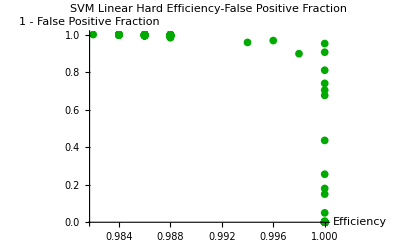

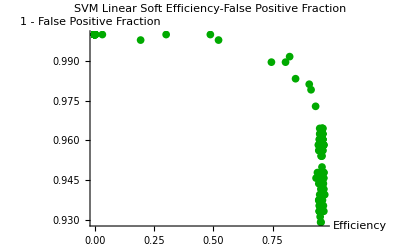

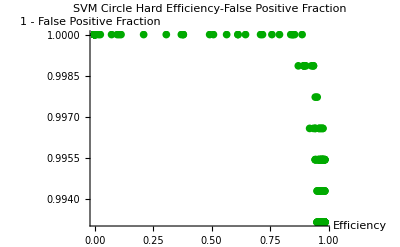

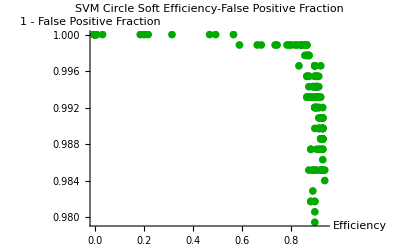

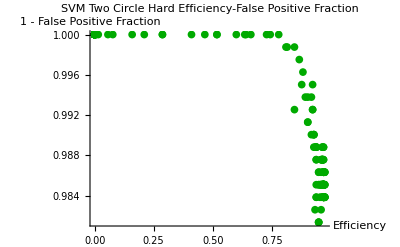

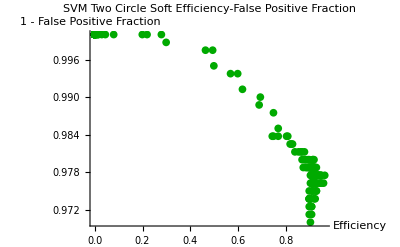

```mathematica
SVMLinearHardEFPPlot
SVMLinearSoftEFPPlot

SVMCircleHardEFPPlot
SVMCircleSoftEFPPlot

SVMTwoCircleHardEFPPlot
SVMTwoCircleSoftEFPPlot
```

#### Efficiency-(1 - False Negative Fraction)

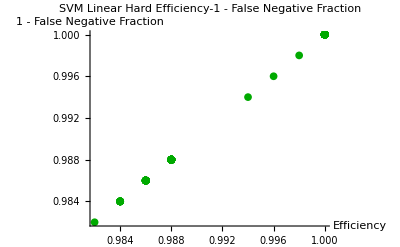

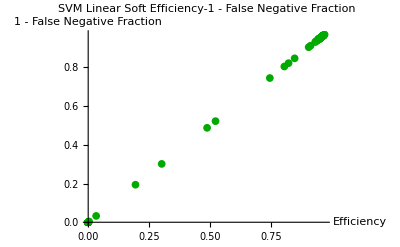

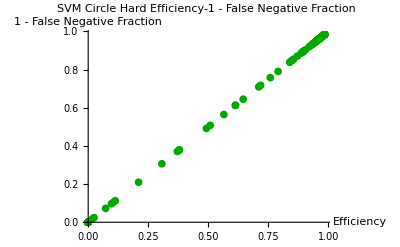

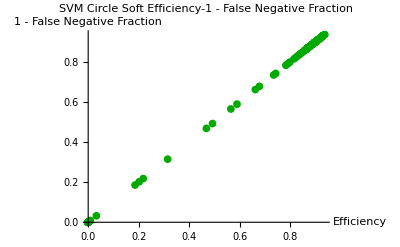

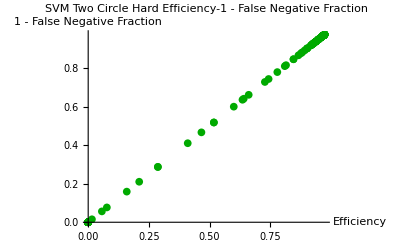

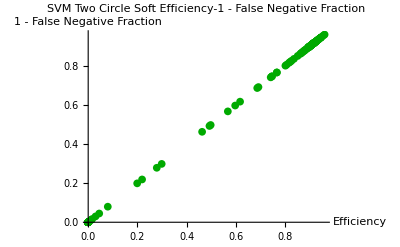

```mathematica
SVMLinearHardEFNPlot
SVMLinearSoftEFNPlot

SVMCircleHardEFNPlot
SVMCircleSoftEFNPlot

SVMTwoCircleHardEFNPlot
SVMTwoCircleSoftEFNPlot
```

#### False Positive Fraction-(1-False Negative Fraction)

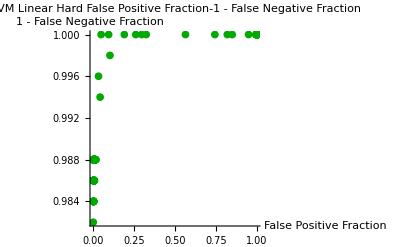

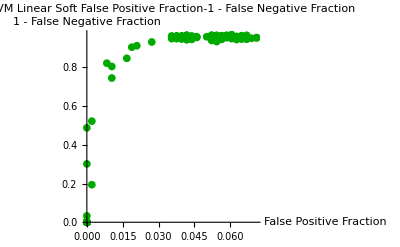

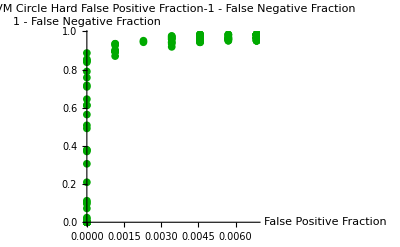

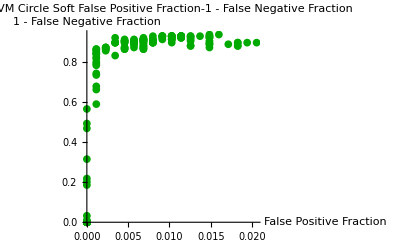

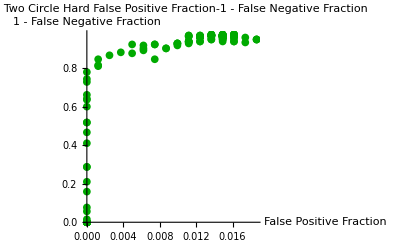

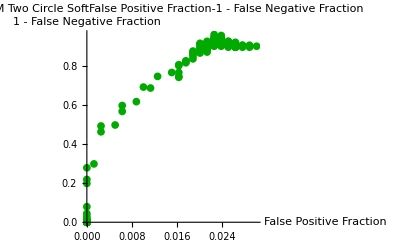

```mathematica
SVMLinearHardFPFNPlot
SVMLinearSoftFPFNPlot

SVMCircleHardFPFNPlot
SVMCircleSoftFPFNPlot

SVMTwoCircleHardFPFNPlot
SVMTwoCircleSoftFPFNPlot
```

### BDS

#### Stumps-Efficiency

```mathematica
BDSLinearHardSEPlot
BDSLinearSoftSEPlot

BDSCircleHardSEPlot
BDSCircleSoftSEPlot

BDSTwoCircleHardSEPlot
BDSTwoCircleSoftSEPlot
```

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDS Linear Hard Stumps-Efficiency,PlotStyle→-Graphics-]

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDS Linear Soft Stumps-Efficiency,PlotStyle→-Graphics-]

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDS Circle Hard Stumps-Efficiency,PlotStyle→-Graphics-]

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDS Circle Soft Stumps-Efficiency,PlotStyle→-Graphics-]

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDS Two Circle Hard Stumps-Efficiency,PlotStyle→-Graphics-]

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDS Two Circle Soft Stumps-Efficiency,PlotStyle→-Graphics-]

#### Efficiency-1 - False Positive Fraction

```mathematica
BDSLinearHardEFPPlot
BDSLinearSoftEFPPlot

BDSCircleHardEFPPlot
BDSCircleSoftEFPPlot

BDSTwoCircleHardEFPPlot
BDSTwoCircleSoftEFPPlot
```

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDS Linear Hard Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDS Linear Soft Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDS Circle Hard Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDS Circle Soft Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDS Two Circle Hard Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDS Two Circle Soft Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

#### Efficiency-1 - False Negative Fraction

```mathematica
BDSLinearHardEFNPlot
BDSLinearSoftEFNPlot

BDSCircleHardEFNPlot
BDSCircleSoftEFNPlot

BDSTwoCircleHardEFNPlot
BDSTwoCircleSoftEFNPlot
```

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDS Linear Hard Efficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDS Linear Soft fficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDS Circle Hard Efficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDS Circle Soft Efficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDS Two Circle Hard Efficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDS Two Circle Soft Efficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

#### False Positive Fraction-1 - False Negative Fraction

```mathematica
BDSLinearHardFPFNPlot
BDSLinearSoftFPFNPlot

BDSCircleHardFPFNPlot
BDSCircleSoftFPFNPlot

BDSTwoCircleHardFPFNPlot
BDSTwoCircleSoftFPFNPlot
```

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Linear Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Linear Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Circle Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Circle Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Two Circle Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Two Circle Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

### BDT

#### Trees-Efficiency

```mathematica
BDTLinearHardTEPlot
BDTLinearSoftTEPlot

BDTCircleHardTEPlot
BDTCircleSoftTEPlot

BDTTwoCircleHardTEPlot
BDTTwoCircleSoftTEPlot
```

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDT Linear Hard Trees-Efficiency,PlotStyle→-Graphics-]

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDT Linear Soft Tres-Efficiency,PlotStyle→-Graphics-]

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDT Circle Hard Trees-Efficiency,PlotStyle→-Graphics-]

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDT Circle Soft Trees-Efficiency,PlotStyle→-Graphics-]

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDT Two Circle Hard Trees-Efficiency,PlotStyle→-Graphics-]

ListPlot[Symbol[],AxesLabel→{Stumps,Efficiency},PlotLabel→BDT Two Circle Soft Trees-Efficiency,PlotStyle→-Graphics-]

#### Efficiency-1 - False Positive Fraction

```mathematica
BDTLinearHardEFPPlot
BDTLinearSoftEFPPlot

BDTCircleHardEFPPlot
BDTCircleSoftEFPPlot

BDTTwoCircleHardEFPPlot
BDTTwoCircleSoftEFPPlot
```

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDT Linear Hard Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDT Linear Soft Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDT Circle Hard Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDT Circle Soft Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDT Two Circle Hard Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Positive Fraction},PlotLabel→BDT Two Circle Soft Efficiency-1 - False Positive Fraction,PlotStyle→-Graphics-]

#### Efficiency-1 - False Negative Fraction

```mathematica
BDTLinearHardEFNPlot
BDTLinearSoftEFNPlot

BDTCircleHardEFNPlot
BDTCircleSoftEFNPlot

BDTTwoCircleHardEFNPlot
BDTTwoCircleSoftEFNPlot
```

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDT Linear Hard Efficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDT Linear Soft fficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDT Circle Hard Efficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDT Circle Soft Efficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDT Two Circle Hard Efficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{Efficiency,1 - False Negative Fraction},PlotLabel→BDT Two Circle Soft Efficiency-1 - False Negative Fraction,PlotStyle→-Graphics-]

#### False Positive Fraction-1 - False Negative Fraction

```mathematica
BDTLinearHardFPFNPlot
BDTLinearSoftFPFNPlot

BDTCircleHardFPFNPlot
BDTCircleSoftFPFNPlot

BDTTwoCircleHardFPFNPlot
BDTTwoCircleSoftFPFNPlot
```

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Linear Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Linear Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Circle Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Circle Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Two Circle Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Two Circle Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-]

### Merged

#### False Positive Fraction- 1 - False Negative Fraction

```mathematica
Show[SVMLinearHardFPFNPlot,BDSLinearHardFPFNPlot,BDTLinearHardFPFNPlot,PlotRange-> All]
Show[SVMLinearSoftFPFNPlot,BDSLinearSoftFPFNPlot,BDTLinearSoftFPFNPlot,PlotRange-> All]

Show[SVMCircleHardFPFNPlot,BDSCircleHardFPFNPlot,BDTCircleHardFPFNPlot,PlotRange-> All]
Show[SVMCircleSoftFPFNPlot,BDSCircleSoftFPFNPlot,BDTCircleSoftFPFNPlot,PlotRange-> All]

Show[SVMTwoCircleHardFPFNPlot,BDSTwoCircleHardFPFNPlot,BDTTwoCircleHardFPFNPlot,PlotRange-> All]
Show[SVMTwoCircleSoftFPFNPlot,BDSTwoCircleSoftFPFNPlot,BDTTwoCircleSoftFPFNPlot,PlotRange-> All]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Linear Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Linear Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],PlotRange→All]

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Linear Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Linear Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],PlotRange→All]

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Circle Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Circle Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],PlotRange→All]

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Circle Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Circle Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],PlotRange→All]

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Two Circle Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Two Circle Hard False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],PlotRange→All]

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDS Two Circle Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],ListPlot[MapAt[1-#1&,Symbol[],{All,2}],AxesLabel→{False Positive Fraction,1 - False Negative Fraction},PlotLabel→BDT Two Circle Soft False Positive Fraction-1 - False Negative Fraction,PlotStyle→-Graphics-],PlotRange→All]